# Mathematica Homework II

Dimitri Leggas & Brian Carlson 2-12-2014

## 1. Consecutive Squares

### Problem:

Write a function called uConsecutiveSquares[low,high] that is given two positive integers as parameters and that returns a list of all the consecutive squares. Each element in the list provides information about one consecutive square in the following form:{n,n^2,(n+1)^2,{list of digits}}.

### Solution:

```mathematica
uConsecutiveSquares[low_,high_]:= Module[{lst={}}(*Forms our list to be returned*)
,For[i = low,i≤ high (*Runs until i = high*)
,If[ Sort[IntegerDigits[i^2]]== Sort[IntegerDigits[(i+1)^2]](*Get the digits from each integer and put them in the same order for comparision of digits*)
,AppendTo[lst,{i,i^2,(i+1)^2,Sort[IntegerDigits[i^2]]}]
(*Add the integer values of i, i^2, and (i+1)^2, as well as the list of digits they share in common*)
]
,i++(*Increment our counter*)
];
Return[lst](*Return our list*)
]
```

```mathematica
uConsecutiveSquares::usage="uConsecutiveSquares[low,high] adds the consecutive squares from low to high returning a list of lists, each containing {n,n^2,(n+1)^2,{List of digits}}, where n  is equal to the first number being squared."
```

uConsecutiveSquares[low,high] adds the consecutive squares from low to high returning a list of lists, each containing {n,n^2,(n+1)^2,{List of digits}}, where n  is equal to the first number being squared.

```mathematica
?uConsecutiveSquares
```

uConsecutiveSquares[
StyleBox["low",
FontFamily->"Mathematica5",
FontWeight->"Plain"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox["high",
FontFamily->"Mathematica5",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Italic"] adds the consecutive squares from 
StyleBox["low",
FontFamily->"Mathematica5",
FontWeight->"Plain",
FontSlant->"Italic"] to 
StyleBox["high",
FontFamily->"Mathematica5",
FontSlant->"Italic"]
StyleBox[" ",
FontFamily->"Mathematica5",
FontSlant->"Italic"]
StyleBox["returning",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["a",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["list",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["of",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["lists",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[",",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["each",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["containing",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["{",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["n",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[",",
FontFamily->"Courier New",
FontWeight->"Plain"]SuperscriptBox[
 StyleBox["n",
FontFamily->"Courier New",
FontWeight->"Plain"], "2"],(n+1)^2,{List of digits}}, where 
StyleBox["n",
FontFamily->"Mathematica5",
FontSize->13,
FontWeight->"Bold",
FontSlant->"Plain",
FontVariations->{"StrikeThrough"->False,
"Underline"->False}]
StyleBox["  ",
FontFamily->"Mathematica5",
FontSize->13,
FontWeight->"Bold",
FontSlant->"Plain",
FontVariations->{"StrikeThrough"->False,
"Underline"->False}]
StyleBox["is",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["equal",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["to",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["the",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["first",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["number",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["being",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[" ",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox["squared",
FontFamily->"Courier New",
FontWeight->"Plain"]
StyleBox[".",
FontFamily->"Courier New",
FontWeight->"Plain"]

#### Test Cases:

```mathematica
uConsecutiveSquares[2,1000]
```

{{13,169,196,{1,6,9}},{157,24649,24964,{2,4,4,6,9}},{913,833569,835396,{3,3,5,6,8,9}}}

```mathematica
uConsecutiveSquares[4,200]
```

{{13,169,196,{1,6,9}},{157,24649,24964,{2,4,4,6,9}}}

## 2. Four Digit Numbers (Kaprekar’s Constant)

### Problems:

For a four digit number x, rearrange the digits from largest to smallest to form a number y and then from smallest to largest to form a number z. Now take y-z. Perform this same operation on the resulting integer until the number 4176 is reached.

(i) Write a function uNextNumber[x] which is given a positive 4-digit integer and which returns the value of   y-z (as described above).

(ii) Write a function uNextNumberSeq[x,count] which is given a positive 4-digit integer x and a second positive integer count . The function returns a list {x_1,x_(2,)x_3,...,x_count} where x_1= x and x_(i+1)=uNextNumber[x_i].

(iii) Test out what happens if you run uNextNumberSeq[x,n] for various starting values for x and various values of n. Collect enough data and look for patterns. Once you found one, formulate a conjecture and support with plenty of data.  Be creative and investigate anything you can think of. It will take some time for you to start thinking outside the box. We expect you to find and describe several well-supported conjectures. 

(iv) Prove (some of) your conjectures.  A proof is a logically convincing argument that some thing is true.

(v) Extra Credit: Generalize: What happens with 5 digit numbers? What happens with 6 digit numbers?

### Solutions:

#### Helper Functions:

Returns the number after it’s been sorted from largest to smallest:

```mathematica
getLargeToSmall::usage="getLargeToSmall[x] returns the value of x after it's digits have been sorted from largest to smallest."
```

getLargeToSmall[x] returns the value of x after it's digits have been sorted from largest to smallest.

```mathematica
?getLargeToSmall
```

getLargeToSmall[
StyleBox["x",
FontSlant->"Italic"]] returns the value of
StyleBox[\ 
 StyleBox[" ",
FontSlant->"Italic"]]
StyleBox["x",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]after it's digits have been sorted from largest to smallest.

```mathematica
getLargeToSmall[x_]:= Module[{},
Return[FromDigits[Sort[IntegerDigits[x],Greater ]]] 
]
```

Returns the number sorted from smallest to largest:

```mathematica
getSmallToLarge::usage="getSmallToLarge[x] returns the value of x after it has been sorted from smallest to largest."
```

getSmallToLarge[x] returns the value of x after it has been sorted from smallest to largest.

```mathematica
?getSmallToLarge
```

getSmallToLarge[
StyleBox["x",
FontSlant->"Italic"]
StyleBox["]",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]returns the value of 
StyleBox["x",
FontSlant->"Italic"]
StyleBox[" ",
FontSlant->"Italic"]after it has been sorted from smallest to largest.

```mathematica
getSmallToLarge[x_]:=Module[{},
Return[FromDigits[Sort[IntegerDigits[x]]]]
]
```

Performs the same function as uNextNumber, except for any size number

```mathematica
anyNextNumber::usage="anyNextNumber[x] performs the first iteration of Kaprekar's Routine on x and returns the result."
```

anyNextNumber[x] performs the first iteration of Kaprekar's Routine on x and returns the result.

```mathematica
?anyNextNumber
```

anyNextNumber[
StyleBox["x",
FontSlant->"Italic"]] performs the first iteration of Kaprekar's Routine on 
StyleBox["x",
FontSlant->"Italic"] and returns the result.

```mathematica
anyNextNumber[x_]:= Module[{z=getSmallToLarge[x],y=getLargeToSmall[x],q=Length[IntegerDigits[x]]},
While[y<10^(q-1),If[y==0,Return[0],y= 10y]];
Return[y-z]
]
```

```mathematica
anyNextNumber[9242]
```

7173

Performs the same function as uNextNumberSeq, except for any size number.

```mathematica
anyNextNumberSeq::usage="anyNextNumberSeq[x,count] performs the count iterations of Kaprekar's Routine on x and returns a list containing the value after each iteration."
```

anyNextNumberSeq[x,count] performs the count iterations of Kaprekar's Routine on x and returns a list containing the value after each iteration.

```mathematica
?anyNextNumberSeq
```

anyNextNumberSeq[
StyleBox["x",
FontSlant->"Italic"]
StyleBox[",",
FontSlant->"Italic"]
StyleBox["count",
FontSlant->"Italic"]] performs the 
StyleBox["count",
FontSlant->"Italic"] iterations of Kaprekar's Routine on 
StyleBox["x",
FontSlant->"Italic"] and returns a list containing the value after each iteration.

```mathematica
anyNextNumberSeq[x_,count_]:= Module[{lst={},temp = x,i},
For[i=1, i≤ count,
temp = anyNextNumber[temp];
AppendTo[lst,temp]
,i++
];
Return[lst]
]
```

Returns a list of the results from running uNextNumberSeq with a count of 8 for all the values between “start” and “stop” inclusive.

```mathematica
numberSteps[start_,stop_]:=Module[{lst={},i},
For[i=start,i≤ stop
,AppendTo[lst,uNextNumberSeq[i,8]];
i++;
];
Return[DeleteDuplicates[lst,Sort[#1]==Sort[#2]&]]
]
```

This function creates a treeplot of a list provided excluding any “rule” (number → other number)  that comes from exclude. This style of graph has no lines and denotes zeros with a red arrow and points the direction each number is heading with a big black arrow. Each vertex is labeled, with the number it represents, by tooltip.

```mathematica
makeGraph[list3_,exclude_]:=Module[{lst =Flatten[list3]},
Show[TreePlot[
DeleteCases[
DeleteCases[Flatten[
(Replace[#,{n1_,n2_}->{n1->n2}]&/@DeleteDuplicates[Partition[lst,2,1],Sort[IntegerDigits[#1]]==Sort[IntegerDigits[#2]]&])],exclude->n_],0->n_]
,Center,VertexLabeling-> Tooltip,DirectedEdges-> True,EdgeRenderingFunction->({If[First[#2]==Last[#2],Red,Black],Arrow[#1,3]}&)
]
,ImageSize->Large]
]
```

This function creates a treeplot of a list provided excluding any “rule” (number → other number)  that comes from exclude. This style of graph has lines and directed edges pointing the direction the number is heading.  Each vertex is labeled, with the number it represents, by tooltip.

```mathematica
makeGraphWithLines[list3_,exclude_]:=
Show[TreePlot[
DeleteCases[
DeleteCases[Flatten[
(Replace[#,{n1_,n2_}->{n1->n2}]&/@DeleteDuplicates[Partition[Flatten[list3],2,1],Sort[IntegerDigits[#1]]==Sort[IntegerDigits[#2]]&])],exclude->n_],0->n_]
,Center,VertexLabeling-> Tooltip,DirectedEdges-> True
]
,ImageSize->Large]
```

#### Section (i)

```mathematica
uNextNumber[x_]:= Module[{z=getSmallToLarge[x],y=getLargeToSmall[x]},
While[y<1000,If[y≤ 0,Return[0],y= 10y]];(*To account for leading zeros, we multiply by 10 until the number is greater than 1000*)
Return[y-z] (*Return the large number subtracted from teh second*)
]
```

#### Section (i) Test Cases:

```mathematica
uNextNumber[8148]
```

7353

```mathematica
8841-1488
```

7353

```mathematica
uNextNumber[9910]
```

9711

```mathematica
9910 - 0199
```

9711

```mathematica
uNextNumber[1234]
```

3087

```mathematica
4321-1234
```

3087

#### Section (ii)

```mathematica
uNextNumberSeq[x_,count_]:= Module[{lst={x},temp = x,i},(**)
For[i=1, i< count,(*Run the loop for a number of times specified when the function is used*)
temp = uNextNumber[temp]; (*Run our number through one iteration of uNextNumber*)
AppendTo[lst,temp]; (*Add our function to the list*)
,i++
];
Return[lst] (*Return our list after the form loop is finished running*)
]
```

#### Section (ii) Test Cases:

```mathematica
uNextNumberSeq[1234,8]
```

{1234,3087,8352,6174,6174,6174,6174,6174}

```mathematica
4321-1234
```

3087

```mathematica
3087
```

3087

```mathematica
8730-0378
```

8352

```mathematica
8532-2358
```

6174

```mathematica
uNextNumberSeq[4747,7]
```

{4747,3267,5265,3996,6264,4176,6174}

```mathematica
7744-4477
```

3267

```mathematica
7632-2367
```

5265

```mathematica
6552-2556
```

3996

```mathematica
9963-3699
```

6264

```mathematica
6642-2466
```

4176

```mathematica
7641-1467
```

6174

```mathematica
uNextNumberSeq[8788,7]
```

{8788,999,8991,8082,8532,6174,6174}

```mathematica
uNextNumberSeq[0001,7]
```

{1,999,8991,8082,8532,6174,6174}

```mathematica
uNextNumberSeq[9753,8]
```

{9753,6174,6174,6174,6174,6174,6174,6174}

{9753,6174,6174,6174,6174,6174,6174,6174}

{9753,6174,6174,6174,6174,6174,6174,6174}

#### Section (iii)

First, we started by making a list of all the numbers that led directly to 6174 after a single iteration of Kaprekar’s iteration.

```mathematica
straightTo6174= Select[Table[i,{i,1000,9999}],uNextNumber[#]==6174&]
```

{}

Next, we applied a filter to the list to account for duplicate arrangements of the same numbers, reducing our list’s size down to 20 from 357.

```mathematica
filteredList=DeleteDuplicates[straightTo6174,Sort[IntegerDigits[#1]]==Sort[IntegerDigits[#2]]&]
```

{1036,1137,1247,1357,1467,1577,2006,2046,2248,2358,2468,2578,2688,3056,3359,3469,3579,3689,3799,4066}

```mathematica
Length[straightTo6174]
```

357

```mathematica
Length[filteredList]
```

20

We verified that each of these numbers immediately went to 6174 after a single application of the routine.

```mathematica
uNextNumberSeq[#,7]&/@filteredList
```

{{1036,6174,6174,6174,6174,6174,6174},{1137,6174,6174,6174,6174,6174,6174},{1247,6174,6174,6174,6174,6174,6174},{1357,6174,6174,6174,6174,6174,6174},{1467,6174,6174,6174,6174,6174,6174},{1577,6174,6174,6174,6174,6174,6174},{2006,6174,6174,6174,6174,6174,6174},{2046,6174,6174,6174,6174,6174,6174},{2248,6174,6174,6174,6174,6174,6174},{2358,6174,6174,6174,6174,6174,6174},{2468,6174,6174,6174,6174,6174,6174},{2578,6174,6174,6174,6174,6174,6174},{2688,6174,6174,6174,6174,6174,6174},{3056,6174,6174,6174,6174,6174,6174},{3359,6174,6174,6174,6174,6174,6174},{3469,6174,6174,6174,6174,6174,6174},{3579,6174,6174,6174,6174,6174,6174},{3689,6174,6174,6174,6174,6174,6174},{3799,6174,6174,6174,6174,6174,6174},{4066,6174,6174,6174,6174,6174,6174}}

We also found the sum of each of the digits in the list to test a thought we had.

```mathematica
Sum[i,{i,IntegerDigits[#]}]&/@filteredList
```

{10,12,14,16,18,20,8,12,16,18,20,22,24,14,20,22,24,26,28,16}

From this, we noticed that two of the numbers were divisible by 9. Extracting them from our list, we found that all four digit integers, other than the ones in our unfiltered list (straightTo6174), appeared to pass through a permutation of these numbers before they reach 6174.

```mathematica
Extract[filteredList,Position[Mod[#,9]&/@filteredList,0]]
```

{1467,2358}

To aid in visualizing this, we created multiple graphs with various styles and layer-to-line length ratios.

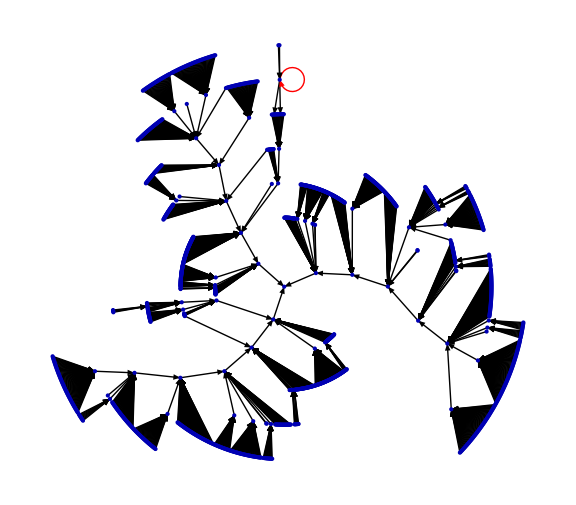

```mathematica
makeGraph[numberSteps[1000,2500],6174]
```

When we ran large amounts of data into the graphing function, the branches leading to 6174 became slightly less clear. To prevent this, we created various graphs with multiple ranges. 
(Note: The circles in the next few plots were consequences of bad coding, but we believed that they didn’t take away from the information that the rest of the graph was displaying, so we kept these versions of the graph in place. In the later plots, you can see where the integer repeating functions lead to: zero.)

```mathematica
makeGraphWithLines[numberSteps[1000,9998],6174]
```

$Aborted

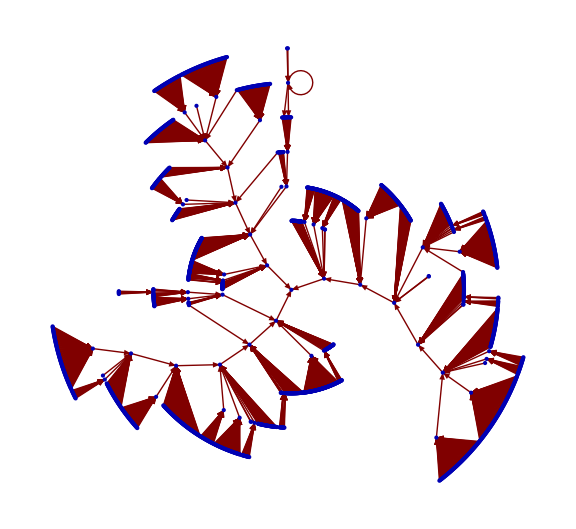

```mathematica
makeGraphWithLines[numberSteps[1000,3000],6174]
```

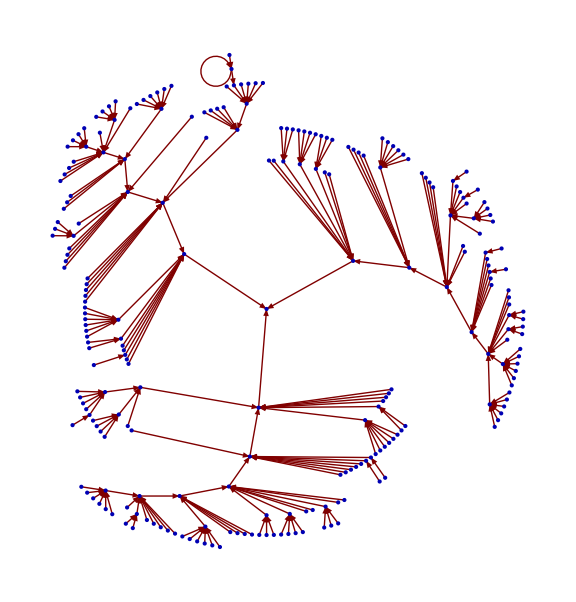

```mathematica
makeGraphWithLines[numberSteps[1000,1200],6174]
```

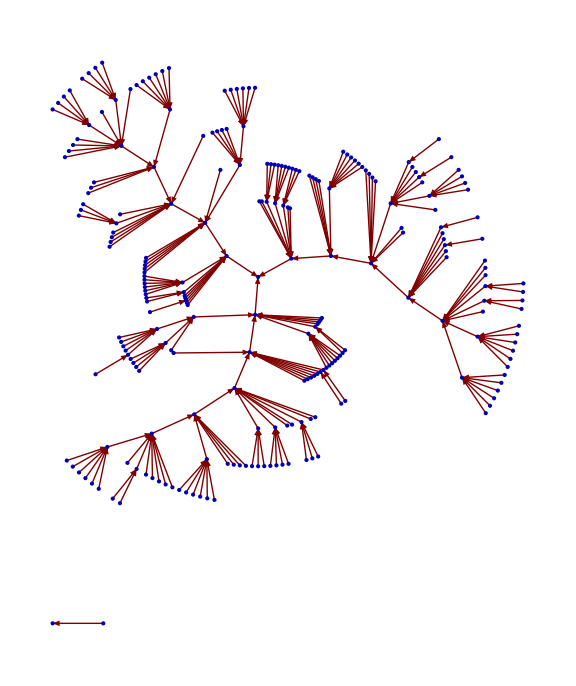

```mathematica
makeGraphWithLines[numberSteps[1000,1200],6174]
```

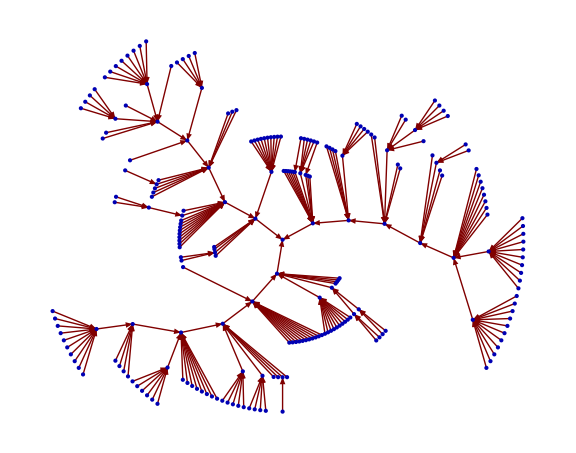

```mathematica
makeGraphWithLines[numberSteps[1200,1400],6174]
```

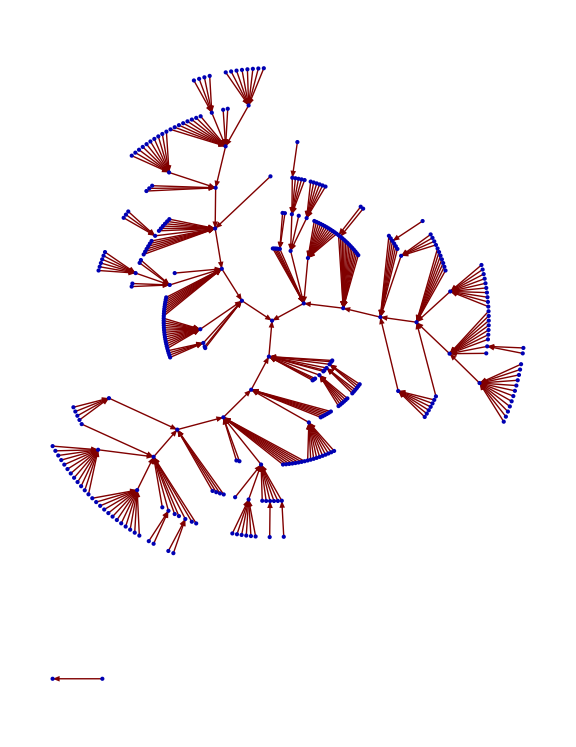

```mathematica
makeGraphWithLines[numberSteps[2000,2300],6174]
```

We counted the number of iterations of Kaprekar’s Routine needed for each function to reach 6174 and played around with the data.

```mathematica
iterations =Module[{lst={},i,x,count=0},
For[i=1000,i≤9999,
If[uNextNumber[i]==0,Continue,
x=i;
While[x≠ 6174,
count++;
x=uNextNumber[x];
];
AppendTo[lst,{i,count}];
count = 0;
]
i++
];
Return[lst]
]
```

Return[{}]

```mathematica
frequency = {Count[#[[2]]&/@iterations,7],Count[#[[2]]&/@iterations,6],Count[#[[2]]&/@iterations,5],Count[#[[2]]&/@iterations,4],Count[#[[2]]&/@iterations,3],Count[#[[2]]&/@iterations,2],Count[#[[2]]&/@iterations,1]}
```

{1980,1508,1379,1124,2124,519,356}

We formed more graphs to help us better visualize this data.

```mathematica
PieChart[frequency,ChartLabels-> {ToString[Round[100*N[#/8999]]]<>"%"&/@frequency},ChartLegends->{"7","6","5","4","3","2","1"},PlotLabel->"Occurence of Iterations Needed to Reach 6174",LabelingFunction->"VerticalCallout",LegendAppearance->{LegendLabel-> "Iterations to reach 6174"}]
```

-Graphics-

We checked for all exceptions to the rule and found that there were only 9.

```mathematica
lst2=numberSteps[1000,9999]
```

{{1000,999,8991,8082,8532,6174,6174,6174},{1001,1089,9621,8352,6174,6174,6174,6174},{1002,2088,8532,6174,6174,6174,6174,6174},{1003,3087,8352,6174,6174,6174,6174,6174},{1004,4086,8172,7443,3996,6264,4176,6174},{1005,5085,7992,7173,6354,3087,8352,6174},{1006,6084,8172,7443,3996,6264,4176,6174},«8987»,{9994,4995,5355,1998,8082,8532,6174,6174},{9995,3996,6264,4176,6174,6174,6174,6174},{9996,2997,7173,6354,3087,8352,6174,6174},{9997,1998,8082,8532,6174,6174,6174,6174},{9998,999,8991,8082,8532,6174,6174,6174},{9999,0,0,0,0,0,0,0}}

```mathematica
lst3=Last[#]==6174&/@lst2
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False}

```mathematica
Position[lst3,False]
```

{{112},{1223},{2334},{3445},{4556},{5667},{6778},{7889},{9000}}

```mathematica
Extract[lst2,Position[lst3,False]]
```

{{1111,0,0,0,0,0,0,0},{2222,0,0,0,0,0,0,0},{3333,0,0,0,0,0,0,0},{4444,0,0,0,0,0,0,0},{5555,0,0,0,0,0,0,0},{6666,0,0,0,0,0,0,0},{7777,0,0,0,0,0,0,0},{8888,0,0,0,0,0,0,0},{9999,0,0,0,0,0,0,0}}

```mathematica
Count[lst3,False]
```

9

#### Section (iv/v)

Unless otherwise specified, a, b, c, and d are the digits of a number where 9≥a,b,c,d≥0.

Conjecture 1: By applying this routine, 6174 maps to itself. Further, 6174 is the only 4 digit number which maps to itself.

Proof:
6174: 7641-1467=7614.
Now, we prove that this is only possible for 6174.
Our goal is to find a 4-digit integer n which results in n after applying this routine. 

Now, let a,b,c,d be the digits of n. Let 9≥a≥b≥c≥d≥0, though equality cannot hold the whole way across, that is, not all the digits can be the same. Now applying the routine we obtain now we apply the routine to find the new number, 1000a+100b+10c+d-(1000d+100c+10b+a), which we will call ABCD. D=10+d-a because a>d (borrowing from next place). C=10+c-1-b=9+c-b because c≥d (borrowing from next place). B=b-1-c. A=a-d.

Note that because A and D are expressed in terms of a and d, A and D cannot correspond to either. For example, if we let A=a then d=0. This implies that there are infinitely many possibilities for D. So A and D must correspond to b and c, then B and C correspond to a and d. 

If we let B=a then b-1-c=a, or b-c=a+1. However, this must be impossible because a≥b,c. Thus, this leaves B=d implying that C=a.

Trying A=b,B=d,C=a,D=c. This yields:
a-d=b
b-1-c=d
9+c-b=a
10+d-a=c

```mathematica
Solve[a-d==b&&b-1-c==d&&9+c-b==a&&10+d-a==c,{a,b,c,d}]
```

{{a→7,b→6,c→4,d→1}}

Substituting we obtain A=6,B=1,C=7,D=4 so n=6174

To prevent missing any other solutions, we try the other option: A=c,B=d,C=a,D=b. This would yield
a-d=c
b-1-c=d
9+c-b=a
10+d-a=b

```mathematica
Solve[a-d==c&&b-1-c==d&&9+c-b==a&&10+d-a==b,{a,b,c,d}]
```

{{a→17/3,b→20/3,c→10/3,d→7/3}}

This solution clearly does not satisfy the conditions of the problem, so 6174 is the only possible solution for n.

Conjecture 2: All numbers generated by this routine are divisible by 9.

Proof:
Let 9≥a≥b≥c≥d≥0 be the digits of some number to which we will apply Kaprekar’s Routine. Therefore our new number will be:
1000a+100b+10c+d-(1000d+100c+10b+a)
=999a+90b-90c-999d
=9(111a+10b-10c-111d)

Conjecture 3: Applying the routine to two numbers that differ by 1 will result in outcomes that differ by predictable values. More specifically:
If 9>a>b>c>d+1>0 for the digits a,b,c,d of the number, that is the new number abc(d+1) contains no repeated digits, then applying the routine to the numbers abcd and abc(d+1) will result in outcomes which differ by 999. 

Proof:
Let 9>a>b>c>d+1>0 for the digits.Then, the two numbers are 1000a+100b+10c+d and 1000a+100b+10c+d+1. Applying the routine to each:
1000a+100b+10c+d-(1000d+100c+10b+a)=999a+90b-90c-999d
1000a+100b+10c+d+1-(1000(d+1)+100c+10b+a)=999a+90b-90c-999(d+1)
Now finding the difference of these two numbers:
999a+90b-90c-999(d+1)-(999a+90b-90c-999d)=-999

Note: In cases where abc(d+1) contains a repeated digit, other difference can be obtained. For example, consider the following mappings:
1243→3087 and 1244→3177. The inputs differ by one, however the outputs differ by 90. The difference of 90 appears to be prevalent, however it appears that the difference depends on which digit is repeated, ie the largest, smallest, etc.

Conjectures 4 and 5: 
(4) Repeated application of the routine always results in 6174, unless the starting number is of the form aaaa where 0≤a≤9, in which case the sequence converges to 0 after the first iteration.
(5) At most, seven iterations are required for the sequence to reach 6174.

Proof: We were not clever enough to prove these conjectures elegantly! Instead we have graphic support of both conjectures in the form of a tree as well as a scan of all the sequences that determined by brute force that these conjectures are correct.

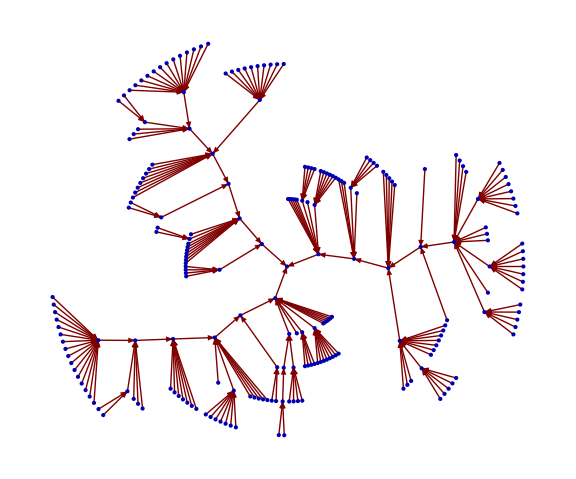

```mathematica
makeGraphWithLines[numberSteps[5000,5200]]
```

By visual inspection and some counting we see that all the numbers in the range 5000-5200 have sequences which terminate in 6174 (hover over nodes to see number!). Further, we can see that the largest number of iterations required was seven. 

We now compute the sequence from this routine for all 4 digit numbers and check to see that the after the seventh iteration the sequence has terminated in 6174. We see that this is only false for the numbers in which all digits are the same.

```mathematica
allNumberSeqs=numberSteps[1000,9999];
seventhIteration=Last[#]==6174&/@allNumberSeqs;
Extract[lst2,Position[seventhIteration,False]]
```

{{1111,0,0,0,0,0,0,0},{2222,0,0,0,0,0,0,0},{3333,0,0,0,0,0,0,0},{4444,0,0,0,0,0,0,0},{5555,0,0,0,0,0,0,0},{6666,0,0,0,0,0,0,0},{7777,0,0,0,0,0,0,0},{8888,0,0,0,0,0,0,0},{9999,0,0,0,0,0,0,0}}

Therefore, all sequences terminate in 6174 by the seventh iteration.

## 3. Twin Primes

### Problem:

How far is it to the next twin prime? A twin prime is a prime number which differs from another prime by two.
Write a function uDistToTwinPrime[number]  which returns the distance to the nearest twin prime.

### Solution:

#### Helper Functions:

This function checks if the entered number is part of a twin prime.

```mathematica
partOfTwinPrime[number_]:= Module[{x=PrimeQ[number]},(*Check if "number" is prime*)
Return[(x&&PrimeQ[number+2])||(x&&PrimeQ[number-2])] (*Check if "number" ±2 is a prime. 
If both checks come out to true, the number is a twin prime*)
]
```

This function finds the number of primes less than or equal to “number” and adds our direction number, “k,” then find the prime number at that value.

```mathematica
nextPrime[number_,k_]:=Module[{},
Return[Prime[PrimePi[number]+k]] 
]
```

This function runs through primes until a twin prime is found.

```mathematica
findNextTwinPrime[number_,direction_]:=Module[{i=number},
While[!partOfTwinPrime[i], 
i=nextPrime[i,direction]
];
Return[i];
]
```

#### Solution Function

```mathematica
uDistToTwinPrime[number_]:=Module[{distance,up=findNextTwinPrime[number,1],down=findNextTwinPrime[number,-1]}
(*"up", denotes the nearest twin prime greater than "number," 
while "down" denotes the nearest twin prime less than "number"*)
,If[up-number<number-down,(*"up-number" denotes the distance to the nearest twin prime greater than "number," 
while "down" denotes the distance to the nearest twin prime less than "number."*)
Return[up-number], (*return whichever distance was considered smallest*)
Return[number-down]
]
]
```

### Test Cases:

#### partOfTwinPrime

Testing 3, 5, 11, 13, 59, 61, which are all parts of twin primes

```mathematica
partOfTwinPrime[3]
partOfTwinPrime[5]
partOfTwinPrime[11]
partOfTwinPrime[13]
partOfTwinPrime[59]
partOfTwinPrime[61]
```

True

True

True

«3 more identical outputs»

Testing 2, 4, 23, 553, 563, which are not part of twin primes (or necessarily prime).

```mathematica
partOfTwinPrime[2]
partOfTwinPrime[4]
partOfTwinPrime[23]
partOfTwinPrime[553]
partOfTwinPrime[563]
```

False

False

False

«2 more identical outputs»

#### nextPrime

```mathematica
nextPrime[2,1]
```

3

```mathematica
nextPrime[3,-1]
```

2

```mathematica
nextPrime[5,2]
```

11

```mathematica
nextPrime[11,-2]
```

5

#### findNextTwinPrime

```mathematica
findNextTwinPrime[2,1] (*Should be 3*)
```

3

```mathematica
findNextTwinPrime[13,1](*Should be 13*)
```

13

```mathematica
findNextTwinPrime[23,1](*Should be 29*)
```

29

```mathematica
findNextTwinPrime[23,-1](*Should be 19*)
```

19

#### uDistToTwinPrime

```mathematica
uDistToTwinPrime[13](*Should be 0*)
```

0

```mathematica
uDistToTwinPrime[23](*Should be 4*)
```

4

```mathematica
uDistToTwinPrime[97](*Should be 4*)
```

4